```mathematica
graph = GraphPlot3D[modules, VertexLabels -> "Name", DirectedEdges->True,ImageSize->800];
graph
```

-Graphics3D-

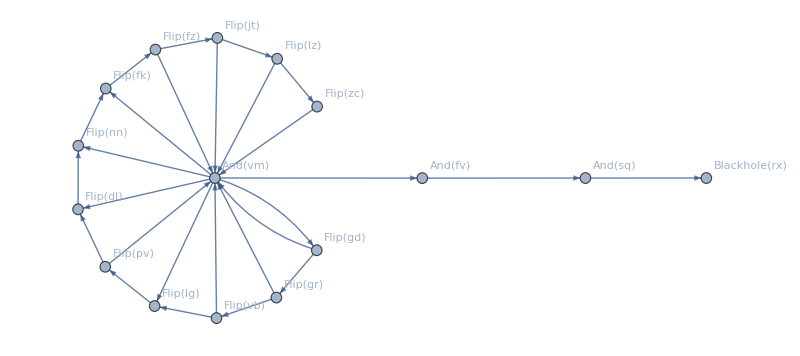
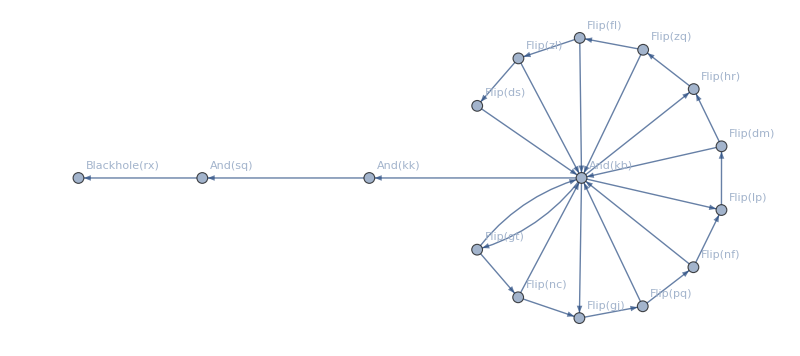
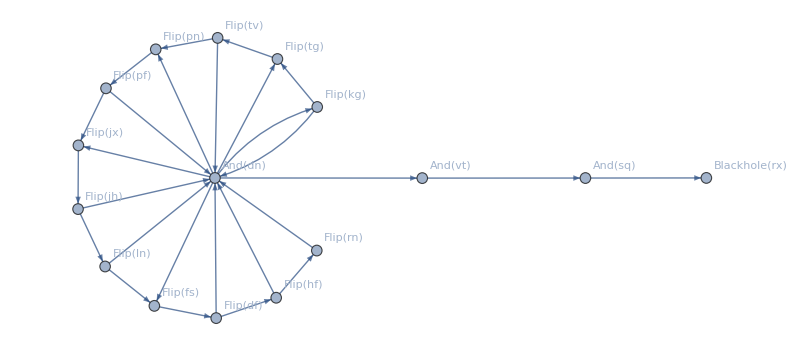
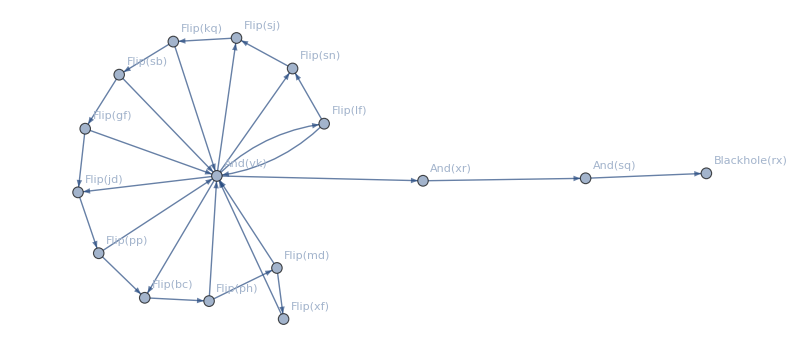

```mathematica
starts={"Flip(gd)","Flip(gt)","Flip(kg)","Flip(lf)"};
limbs=starts//Map[NestGraph[(modules // Cases[(#->v_):>v])&,#,20, VertexLabels -> "Name", DirectedEdges->True,ImageSize->800]&]
```

```mathematica
3769*3797*3931*3863
```

217317393039529

```mathematica
modules={"Flip(bc)" -> "Flip(ph)","Flip(hr)" -> "Flip(zq)","Flip(sn)" -> "Flip(sj)","Flip(df)" -> "And(dn)","Flip(df)" -> "Flip(hf)","Flip(lp)" -> "Flip(dm)","Flip(lf)" -> "Flip(sn)","Flip(lf)" -> "And(vk)","And(fv)" -> "And(sq)","Flip(gd)" -> "And(vm)","Flip(gd)" -> "Flip(gr)","Flip(jt)" -> "And(vm)","Flip(jt)" -> "Flip(lz)","Flip(xf)" -> "And(vk)","Flip(nf)" -> "Flip(lp)","Flip(nf)" -> "And(kb)","Flip(dl)" -> "Flip(nn)","And(sq)" -> "Blackhole(rx)","Flip(vb)" -> "And(vm)","Flip(vb)" -> "Flip(lg)","Flip(zq)" -> "And(kb)","Flip(zq)" -> "Flip(fl)","Flip(fk)" -> "Flip(fz)","Flip(gj)" -> "Flip(pq)","Flip(jx)" -> "Flip(jh)","Flip(pq)" -> "And(kb)","Flip(pq)" -> "Flip(nf)","And(dn)" -> "Flip(kg)","And(dn)" -> "And(vt)","And(dn)" -> "Flip(tg)","And(dn)" -> "Flip(fs)","And(dn)" -> "Flip(pn)","And(dn)" -> "Flip(jx)","Flip(ln)" -> "And(dn)","Flip(ln)" -> "Flip(fs)","Flip(fz)" -> "And(vm)","Flip(fz)" -> "Flip(jt)","Flip(fs)" -> "Flip(df)","Flip(dm)" -> "And(kb)","Flip(dm)" -> "Flip(hr)","Flip(ds)" -> "And(kb)","And(kk)" -> "And(sq)","Flip(tg)" -> "Flip(tv)","And(vt)" -> "And(sq)","Flip(fl)" -> "Flip(zl)","Flip(fl)" -> "And(kb)","And(vk)" -> "Flip(bc)","And(vk)" -> "Flip(sj)","And(vk)" -> "Flip(jd)","And(vk)" -> "Flip(lf)","And(vk)" -> "And(xr)","And(vk)" -> "Flip(sn)","Flip(jd)" -> "Flip(pp)","Flip(tv)" -> "And(dn)","Flip(tv)" -> "Flip(pn)","Flip(sb)" -> "Flip(gf)","Flip(sb)" -> "And(vk)","And(kb)" -> "And(kk)","And(kb)" -> "Flip(gj)","And(kb)" -> "Flip(gt)","And(kb)" -> "Flip(hr)","And(kb)" -> "Flip(lp)","Flip(pp)" -> "And(vk)","Flip(pp)" -> "Flip(bc)","Flip(pn)" -> "Flip(pf)","Flip(zc)" -> "And(vm)","And(vm)" -> "Flip(dl)","And(vm)" -> "Flip(fk)","And(vm)" -> "Flip(nn)","And(vm)" -> "And(fv)","And(vm)" -> "Flip(gd)","And(vm)" -> "Flip(lg)","Flip(rn)" -> "And(dn)","Flip(gr)" -> "Flip(vb)","Flip(gr)" -> "And(vm)","Flip(sj)" -> "Flip(kq)","Flip(zl)" -> "And(kb)","Flip(zl)" -> "Flip(ds)","Flip(lz)" -> "And(vm)","Flip(lz)" -> "Flip(zc)","Flip(jh)" -> "And(dn)","Flip(jh)" -> "Flip(ln)","Flip(pf)" -> "And(dn)","Flip(pf)" -> "Flip(jx)","Flip(kq)" -> "Flip(sb)","Flip(kq)" -> "And(vk)","Flip(ph)" -> "Flip(md)","Flip(ph)" -> "And(vk)","Flip(nc)" -> "Flip(gj)","Flip(nc)" -> "And(kb)","Flip(kg)" -> "Flip(tg)","Flip(kg)" -> "And(dn)","Flip(hf)" -> "And(dn)","Flip(hf)" -> "Flip(rn)","Flip(nn)" -> "Flip(fk)","Flip(gf)" -> "Flip(jd)","Flip(gf)" -> "And(vk)","Flip(lg)" -> "Flip(pv)","Cast" -> "Flip(gd)","Cast" -> "Flip(kg)","Cast" -> "Flip(gt)","Cast" -> "Flip(lf)","Flip(gt)" -> "Flip(nc)","Flip(gt)" -> "And(kb)","Flip(pv)" -> "Flip(dl)","Flip(pv)" -> "And(vm)","And(xr)" -> "And(sq)","Flip(md)" -> "And(vk)","Flip(md)" -> "Flip(xf)","Btn" -> "Cast"};
```